## Cargar Datos

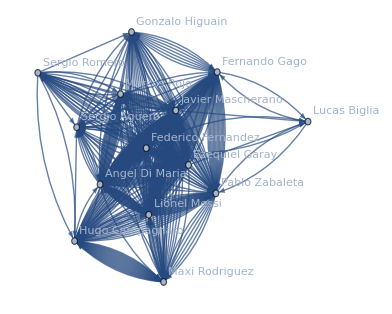
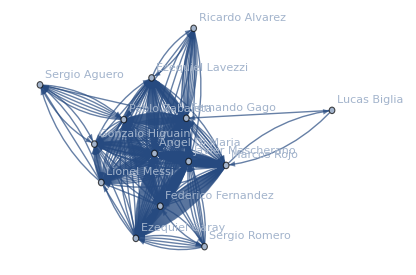
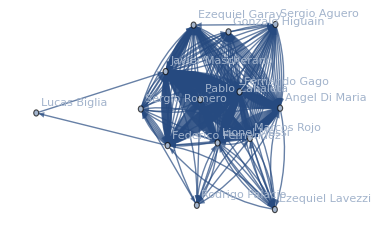
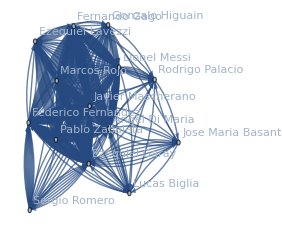
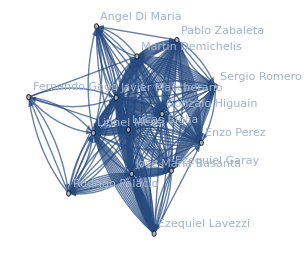
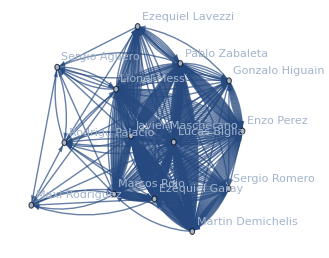
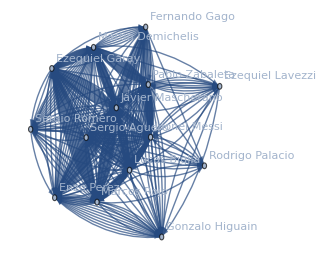

```mathematica
SetDirectory[NotebookDirectory[]];
files = FileNames["*Argentina.txt",{"./fifa_2014_pass_distributions/mathematica_data/networks/"}];
data=ToExpression[Import[#]&/@files];
graphs = Graph[#, VertexLabels->"Name"]&/@data
```

### HIstograma grado para cada red

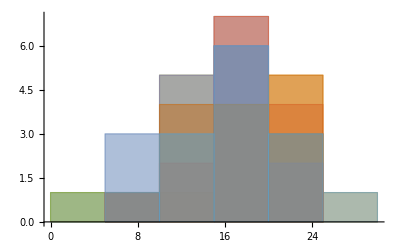

```mathematica
Histogram[DegreeCentrality[#]&/@graphs]
```

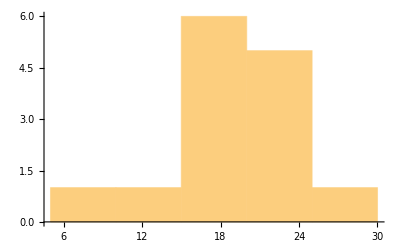
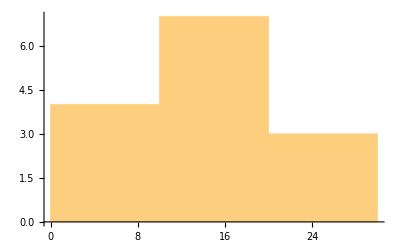
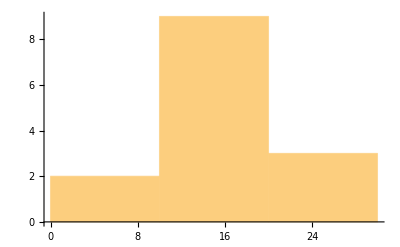
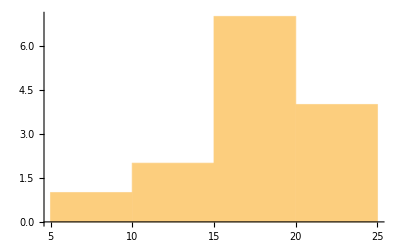
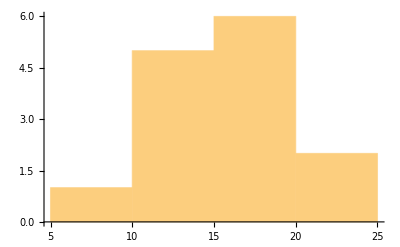
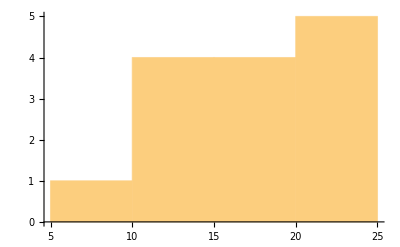
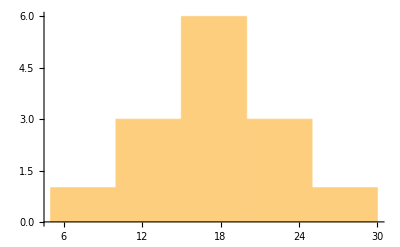

```mathematica
Table[Histogram[DegreeCentrality[graphs[[i]]]], {i, 1, Length[graphs]}]
```

```mathematica
HighlightGraph[#,VertexList[#],VertexSize->Thread[VertexList[#]->Rescale[DegreeCentrality[#]]]]&/@graphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Media grado en una grafica para cada red

```mathematica
mediagrado=Table[Mean[VertexDegree[graphs[[i]]]], {i, 1, Length[graphs]}]
ejeX={1,2,3,4,5,6,7};
```

{536/7,479/7,510/7,587/7,326/7,70,416/7}

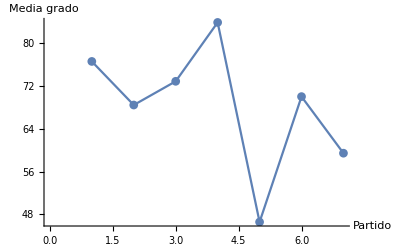

```mathematica
ListPlot[Table[{ejeX[[i]],mediagrado[[i]]},{i,1,Length[graphs]}],AxesLabel->{"Partido","Media grado"},Joined->True,PlotMarkers->Automatic]
```

### Media pathlenght en una grafica para cada red

```mathematica
mediaavpl=Table[N[Mean[Flatten[GraphDistanceMatrix[UndirectedGraph[graphs[[i]]]]]]],{i,1,Length[graphs]}]
```

{1.13265,1.2449,1.20408,1.15306,1.16327,1.11224,1.13265}

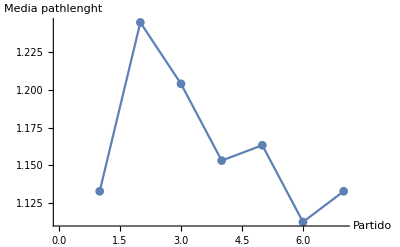

```mathematica
ListPlot[Table[{ejeX[[i]],mediaavpl[[i]]},{i,1,Length[graphs]}],AxesLabel->{"Partido","Media pathlenght"},Joined->True,PlotMarkers->Automatic]
```

### Cada red community plot

```mathematica
Table[CommunityGraphPlot[graphs[[i]]],{i,1,Length[graphs]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
clusteringCoefficienrs = N[GlobalClusteringCoefficient[#]&/@graphs]
```

{0.747953,0.736397,0.655126,0.690428,0.677083,0.711373,0.7}

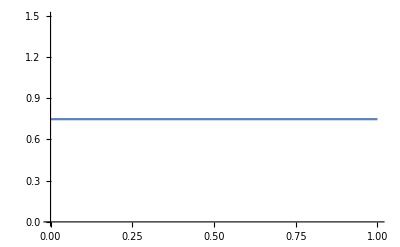
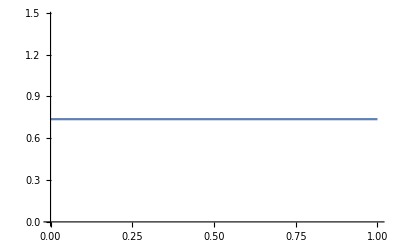
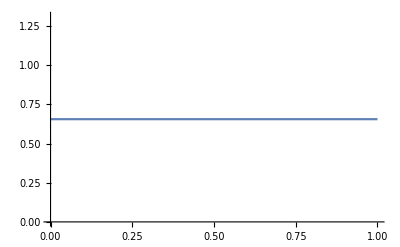
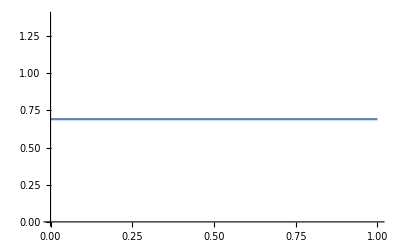
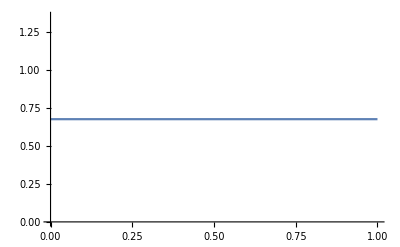
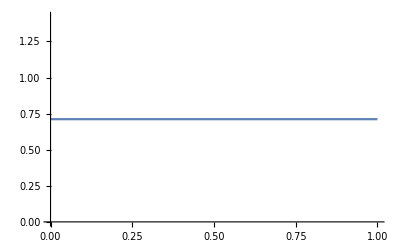
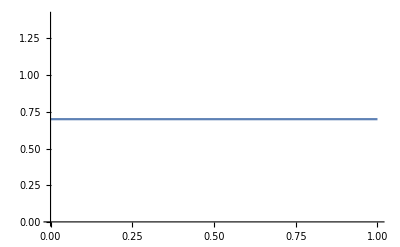

```mathematica
Plot[GlobalClusteringCoefficient[#],{p,0,1},MaxRecursion-> 0]&/@graphs
```